```mathematica
ClearAll["Global`*"]
```

```mathematica
TagList ={"#boston","#bostonmarathon","#bostonstrong","#prayforboston"};
PlotType={VC,VID,CC,GD,GR,GCC,GA,MND,MDC};
S[x_]:=StringSplit[StringReplace[x,{"\""->""}]," -> "];
Fdate[x_]:=DateString[{2013,4,15,(5+x),0,0},{"DayNameShort","Hour12","AMPMLowerCase"}];
```

#### Imports data from files then anaylsises it for 9 charectoristics.

```mathematica
L=96;
For[n=1,n≤4,n++,
T=TagList[[n]];
For[i=1,i≤L,i++,
file="/Users/danielgladstone/Documents/twitter_project/auto_graphing/"<>T<>"1039"<>"/"<>Fdate[i];

If[FileExistsQ[file],

F =Import[file,"List"];

GList[T][i]=DeleteDuplicates[Table[
joined=First[S[F[[j]]]]->Last[S[F[[j]]]]
,{j,1,Length[F]}]];
If[Length[GList[T][i]]≤1,

(*Print["Zero: n="<>ToString[n]<>". i="<>ToString[i]];*)

G[T][i]=0;
G[VC][T][i]=0;
G[VID][T][i]=0;
G[CC][T][i]=0;
G[GD][T][i]=0;
G[GR][T][i]=0;
G[GCC][T][i]=0;
G[GA][T][i]=0;
G[MND][T][i]=0;
G[MDC][T][i]=0;,

G[T][i]=Graph[GList[T][i]];
G[VC][T][i]=VertexCount[G[T][i]];
G[VID][T][i]=Mean[VertexInDegree[G[T][i]]];
G[CC][T][i]=Mean[ClosenessCentrality[G[T][i]]];
G[GD][T][i]=GraphDensity[G[T][i]];
G[GR][T][i]=GraphReciprocity[G[T][i]];
G[GCC][T][i]=GlobalClusteringCoefficient[G[T][i]];
G[GA][T][i]=GraphAssortativity[G[T][i]];
G[MND][T][i]=Mean[MeanNeighborDegree[G[T][i]]];
G[MDC][T][i]=Mean[MeanDegreeConnectivity[G[T][i]]];
];
,
G[T][i]=0;
G[VC][T][i]=0;
G[VID][T][i]=0;
G[CC][T][i]=0;
G[GD][T][i]=0;
G[GR][T][i]=0;
G[GCC][T][i]=0;
G[GA][T][i]=0;
G[MND][T][i]=0;
G[MDC][T][i]=0;]
]]
```

#### Iterate over data to become listed and graphable data.

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type*)

GT=PlotType[[p]];

data=
Table[
T=TagList[[n]];(*What hashtag are we looking at*)
Table[
G[GT][T][i],{i,L}] (*Iterate over every time period*)
,{n,1,4}]; (*Iterate over each hashtag*)

Data[GT]=data; (*list of data for a given graph type in with composed of smaller list for each hashtag*)
]
```

#### Iterate over data and time to become listed and graphable data with time on X-axis.

```mathematica
For[p=1,p≤9,p++,(*iterate over each graph type*)

GT=PlotType[[p]];

Tdata=Table[(*iterate over each tag*)
Table[(*iterate over each date**)
{Fdate[i],Data[VC][[n]][[i]]}
,{i,L}]
,{n,4}];
TData[GT]=Tdata;
]
bpd=Table[
GT=PlotType[[p]];
DateListPlot[
Table[TData[GT][[n]],{n,4}],{Fdate[1],Fdate[L]},PlotLegends->TagList,PlotLabel->GT],{p,9}];
```

#### Finds a function which corresponds to the 4 hashtags and 9 charectoristics associated with each tag.

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type basicly decomposing the previous Data*)

GT=PlotType[[p]];

fun=
Table[
Fit[
Table[
{i,Data[GT][[n]][[i]]},{i,L}](*Iterate over every time period*)
,{1,x,x^2,x^3,x^4,x^5,x^6},x](*how to find line in data*)
,{n,4}];(*iterate over each hashtag*)
Fun[GT]=fun;
]
```

#### Plots the data and corresponding functions.

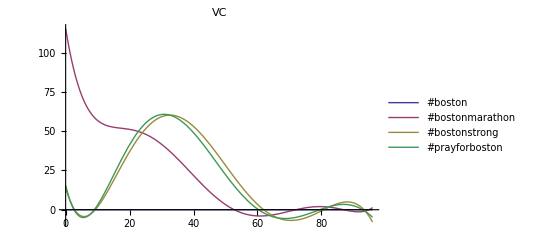
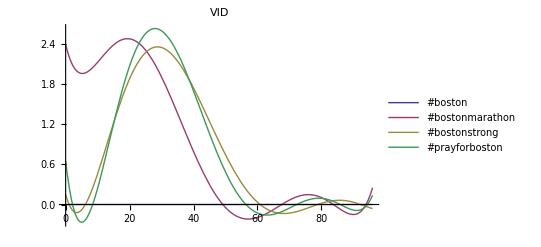
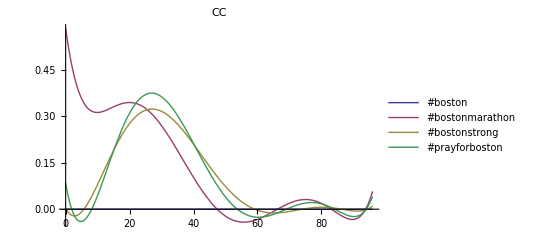
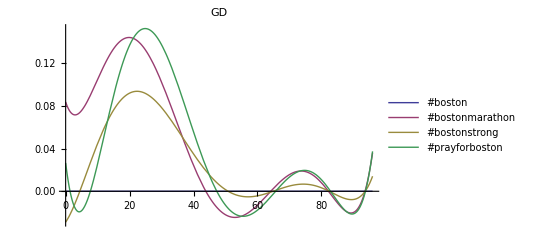
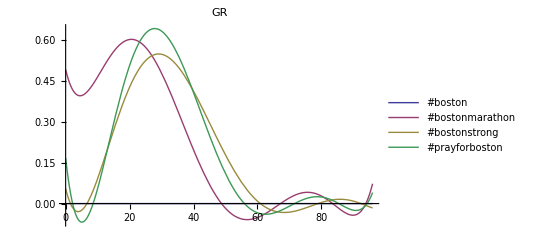
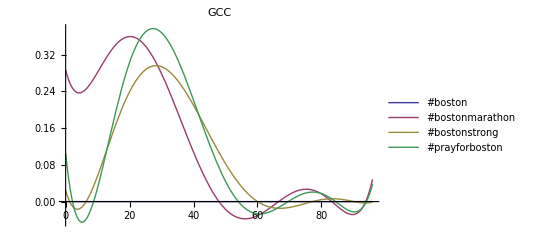
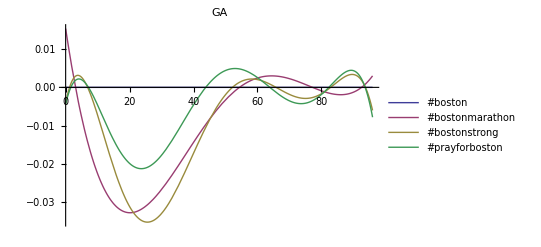
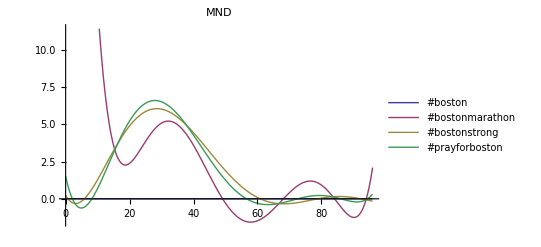

```mathematica
Table[
GT=PlotType[[p]];
f=Fun[GT];
Plot[f,{x,0,L},PlotLegends->TagList, PlotLabel->GT],{p,9}]
```

```mathematica
3
```

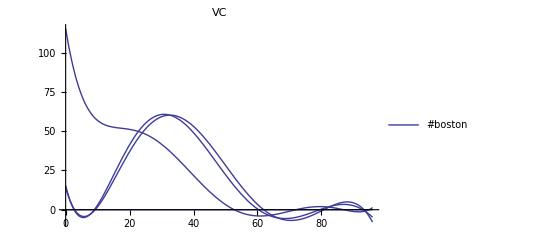
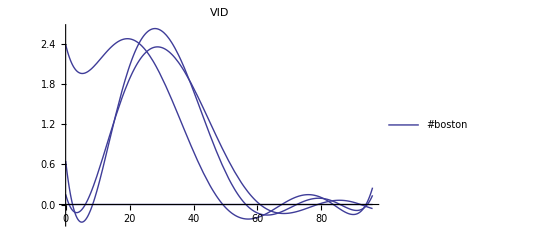
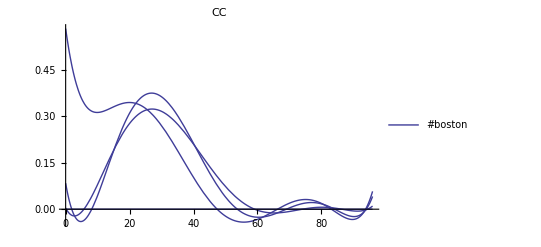
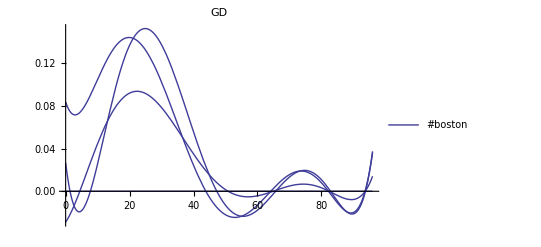
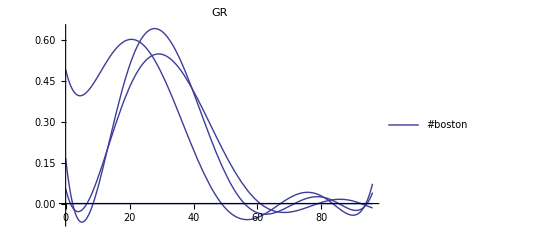
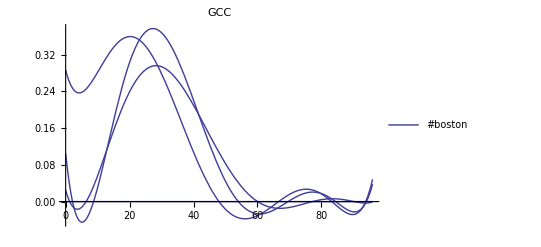
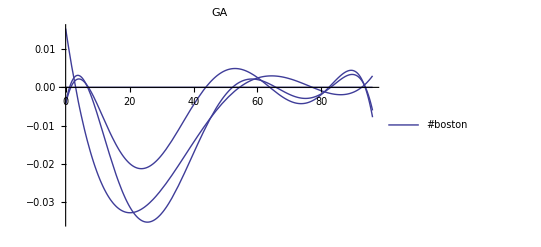
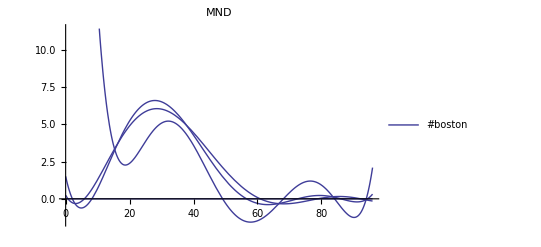

```mathematica
Table[
GT=PlotType[[p]];
bp=Plot[Fun[GT],{x,0,L},PlotLegends->TagList,PlotLabel->GT];
bpl=ListPlot[Data[GT],PlotLegends->TagList,PlotLabel->GT];
bp,{p,9}]
```

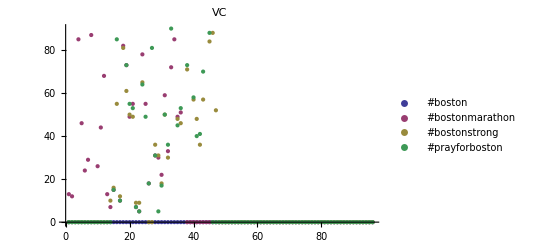
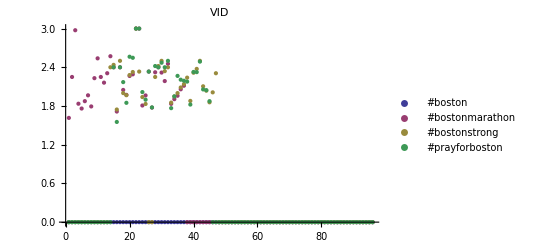
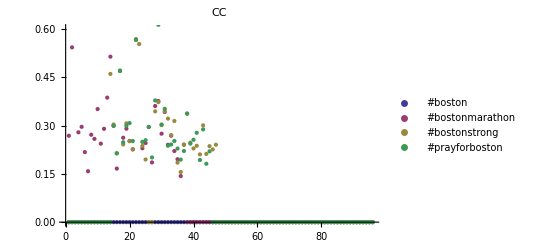
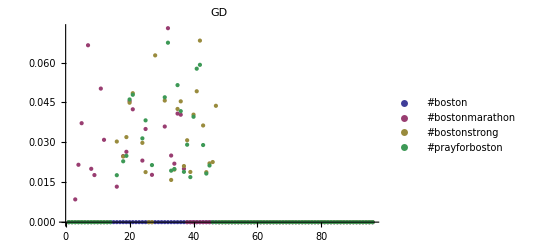
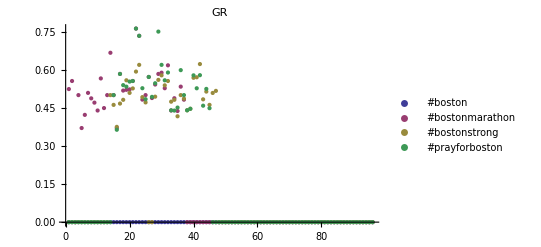
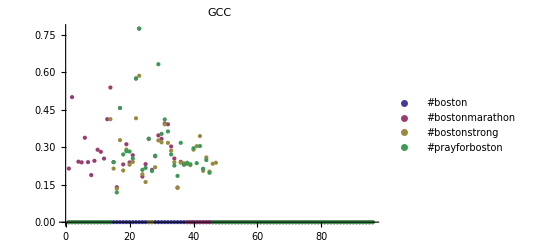
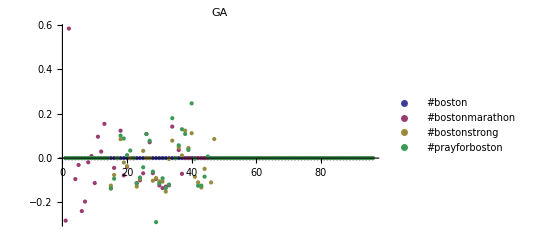
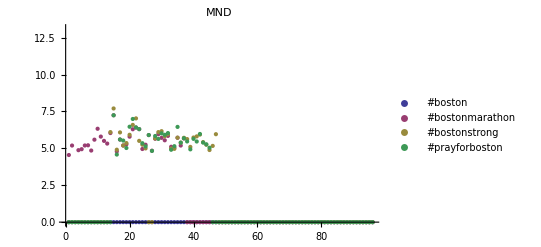

```mathematica
lp=Table[
ListPlot[d[type[[o]]],PlotLabel->type[[o]], PlotLegends->Table[
TList[[t]],{t,1,4}]]
,{o,9}]

md=Table[Fit[d[type[[1]]][[j]],{1,x},x],{j,4}];

min=Min[Table[d[type[[1]]][[j]],{j,4}]];
max = Max[Table[d[type[[1]]][[j]],{j,4}]];
Plot[md,{x,min,max}]

(*
Table[
d[type[[1]]][[j]],{j,4}];

Show[lp,Plot[md,{x,min,max}]]*)
```

```mathematica
VertexInDegree[G[T[[3]]][2]]
```

{}

```mathematica
.
```

```mathematica
G=Graph[GList]

VertexCount[G]
Mean[VertexInDegree[G]]
Mean[ClosenessCentrality[G]]
GraphDensity[G]
GraphReciprocity[G]
GlobalClusteringCoefficient[G]
GraphAssortativity[G]
Mean[MeanNeighborDegree[G]]
Mean[MeanDegreeConnectivity[G]]
```

-Graphics-

4

2

0.9375

2/3

3/4

3/5

0

9/2

7/3

```mathematica
First[F[[1]]]->Last[F[[1]]]
```

#cat→#cats

```mathematica
.
```

```mathematica
Table[
Print[i];
,{i,2,5}]
```

2

3

4

5

{Null,Null,Null,Null}